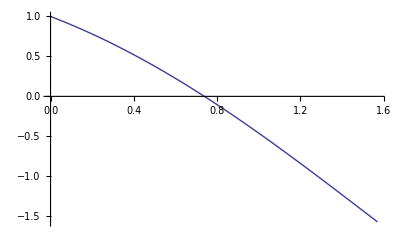

```mathematica
g[x_]:=Cos[x]-x
Plot[g[x],{x,0,π/2}]
```

```mathematica
dicho[f_,a1_,b1_,eps_]:=
Module[{a=a1,b=b1,c},
While[b-a>eps,c=(a+b)/2;If[f[a]*f[c]≤0,b=c,a=c]];Print[a,b]]
```

```mathematica
dicho[g,0,Pi/2,0.001]
```

(963 π)/4096(241 π)/1024